-Graphics-

# Solution of Coupled Differential Equations Describing The Time Evolution of a System of Three Interchanging Species

This notebook has been created with Mathematica Commercial License L3302-6545 .

June 23, 2020

Copyright (c) David M. Morgan, Ph.D.
GNU General Public License, v. 3.0 or later

Antigonish Landing, NS B2G 2L2 Canada
dmmorgan@gmail.com
(902) 318-4906

System:

-Graphics-

#### Set of Coupled Differential Equations Describing the Time - Evolution of the System :

The concentration of species A, [A], decreases over time as it spontaneously converts to B with rate = -k_1[A]. It is disappearing, so this term is negative. It also disappears as it converts to C with a rate = -k_-3[A]; [A] increases as B reconverts back to A with rate = +k_-1[B], and as C reconverts back to A with rate = +k_3[C]. These ideas are expressed formally as the differential equation (1). Equations (2) and (3) may be found similarly.  

(1)	ⅆ/ⅆt[A] = -(k_1 + k_-3) [A] + k_-1 [B] + k_3 [C]

(2)	ⅆ/ⅆt[B] = k_1[A] - (k_2 + k_-1) [B] + k_-2 [C] 

(3)	ⅆ/ⅆt[C] =  k_-3 [A] + k_2 [B] - (k_2 + k_3) [C]

Define these as the linear, constant coefficient, matrix equation ⅆ/ⅆt u⃗ = AA u⃗, 

in which u⃗ = ([A]
[B]
[C]) and AA = (-(k_1+k_-3) | k_-1  | k_3 
k_1 | -(k_2+k_-1)  | k_-2 
k_-3  | k_2  | -(k_-2+k_3)).

#### Problem:

Find u⃗(t) for a given set of boundary conditions u⃗(0).

Principle: 

For  ⅆ/ⅆt u⃗ = AA u⃗, 

if AA x⃗ = λ x⃗, then 

ⅆ/ⅆt x⃗ = λ e^(λ t) x⃗, 

in which λ is an eigenvalue of the matrix and x⃗ is the corresponding eigenvector.

#### Set up the chemical problem :

Define rate constants, provide immediate values for them.

```mathematica
rateconstants = {
Subscript[k, 1] -> 150,
Subscript[k, -1] -> 5,
Subscript[k, 2] -> 500,
Subscript[k, -2] -> 1,
Subscript[k, 3] -> .01,
Subscript[k, -3] -> .05
}
```

{k_1→150,k_-1→5,k_2→500,k_-2→1,k_3→0.01,k_-3→0.05}

Define the initial conditions,  u⃗:

```mathematica
initialconcentrations = {
aa -> .001,
bb -> 0,
cc -> 0
};

Subscript[u⃗, 0]= {aa, bb, cc}/. initialconcentrations;

Subscript[u⃗, 0]//MatrixForm
```

(0.001
0
0)

Solution - Theory:

We have  ⅆ/ⅆt u⃗ = AA u⃗. 

Now, with respect to the derivative, substitute u⃗ → e^(λ t) x⃗, and compute the resulting derivative: 

ⅆ/ⅆt u⃗; 		u⃗ → e^(λ t) x⃗

ⅆ/ⅆt u⃗ → ⅆ/ⅆt(e^(λ t) x⃗)

ⅆ/ⅆt(e^(λ t) x⃗) = λ e^(λ t) x⃗

Notice that if one makes the reverse substitution, e^(λ t) x⃗ → u⃗  

λ e^(λ t) x⃗;	e^(λ t) x⃗ → u⃗

λ e^(λ t) x⃗ → λ u⃗

if u⃗ is an eigenvector, then

AA u⃗ =  λ u⃗

Therefore, for x⃗ which are eigenvectors of AA, the set of eigenvector equations e^(λ t) x⃗ are “pure exponential” solutions. The solution to the chemical problem, however, is multi-exponential, and is found by solving for the linear combination that satisfies the initial conditions: 

∑_(i=1)^n C_i (x⃗)_i= u⃗(0)

Solution - Computation thereof:

Define AA.

```mathematica
AA = {
{-(Subscript[k, 1]+ Subscript[k, -3]),Subscript[k, -1], Subscript[k, 3] },
{Subscript[k, 1],-(Subscript[k, 2]+Subscript[k, -1]), Subscript[k, -2]},
{Subscript[k, -3], Subscript[k, 2], -(Subscript[k, -2]+Subscript[k, 3])}
}/. rateconstants;

(* comment out the rateconstants substitution for a theoretical solution *)

AA//MatrixForm
```

(-150.05 | 5 | 0.01
150 | -505 | 1
0.05 | 500 | -1.01)

Find the eigenvalues and eigenvectors of AA.

x⃗ is an eigenvector of AA if

AA x⃗ = λ x⃗,

and λ is the corresponding eigenvalue. 

Rearranging provides: 

AA x⃗ = λ x⃗

AA x⃗- λ x⃗ = OverVector[0]

(AA - λ II) x⃗ = OverVector[0]

in which II is the identity matrix. Rejecting the useless solution x⃗ = OverVector[0], this equation is only true when AA - λ II is not invertible, meaning its determinant must = 0. 

det(AA - λ II) = 0, 

which provides the characteristic equation of the matrix.

Find the characteristic equation:

```mathematica
{{"\t\t\tAA:", "Identity Matrix:"},{AA//MatrixForm, IdentityMatrix[3]//MatrixForm}}//TableForm

{"\t\t\t\tAA - evalue II:", {AA - evalue IdentityMatrix[3]//MatrixForm}}//TableForm

{"Characteristic equation:",
"det(AA - evalue II) = 0"}//TableForm
```

AA: | Identity Matrix:
(-150.05 | 5 | 0.01
150 | -505 | 1
0.05 | 500 | -1.01) | (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

AA - evalue II:
(-150.05-evalue | 5 | 0.01
150 | -505-evalue | 1
0.05 | 500 | -1.01-evalue)

Characteristic equation:
det(AA - evalue II) = 0

```mathematica
ceqnmtx = AA - evalue IdentityMatrix[3];
ceqn = Det[ceqnmtx]
```

0.-75186.9 evalue-656.06 evalue^2-evalue^3

Set the characteristic equation = 0 and solve for evalue:

```mathematica
lambdasubs = Solve[ceqn == 0, evalue];
lambdasubs[[3,1,2]] = Re[lambdasubs[[3,1,2]]];
lambdasubs
```

{{evalue→-508.077},{evalue→-147.983},{evalue→0.}}

Verify with Mathematica’s Eigenvalues[] function:

```mathematica
Eigenvalues[AA]
```

{-508.077,-147.983,-2.59778×10^-16}

Note that the third eigenvalue in both solutions is a rounding error;  the theoretical result is 0. The reader may demonstrate this by repeating  the method up to this point, except commenting out the substitution of the rate constants (“ /. rateconstants”) in the definition of AA.   


Find eigenvectors. 

For each λ, solve:

det(AA - λ II) = 0 

and use the resulting set of equations to solve for the components of the eigvenvector.

For λ = -1005.8: 

(AA + 1005.8 II) x⃗ = OverVector[0]

```mathematica
RowReduce[(AA - λ IdentityMatrix[3])/. λ ->  lambdasubs[[1,1,2]]]//MatrixForm
```

(1 | 0. | -0.0141349
0 | 1 | 1.01413
0 | 0 | 0)

Provides

```mathematica
ev1 = {-%[[1,3]], -%[[2,3]], 1}
```

{0.0141349,-1.01413,1}

AA ev1:

```mathematica
AA . ev1
```

{-7.18162,515.258,-508.077}

For λ = -150.304: 

(AA + 150.304 II) x⃗ = OverVector[0]

```mathematica
RowReduce[(AA - λ IdentityMatrix[3])/. λ ->  lambdasubs[[2,1,2]]]//MatrixForm
```

(1 | 0. | 0.706124
0 | 1 | 0.293876
0 | 0 | 0)

Provides

```mathematica
ev2 = {-%[[1,3]], -%[[2,3]], 1}
```

{-0.706124,-0.293876,1}

```mathematica
AA . ev2
```

{104.495,43.4887,-147.983}

For λ = -0: 

(AA - 0 II) x⃗ = OverVector[0]

```mathematica
Re[
RowReduce[(AA - λ IdentityMatrix[3])/. λ ->  lambdasubs[[3,1,2]]]]//MatrixForm
```

(1 | 0. | -0.000133955
0 | 1 | -0.00201999
0 | 0 | 0)

Provides

```mathematica
ev3 = {-%[[1,3]], -%[[2,3]], 1}
```

{0.000133955,0.00201999,1}

Check using Mathematica’s Eigenvectors[] function.

```mathematica
wolframev = Eigenvectors[AA]
```

{{0.00992401,-0.712017,0.702093},{-0.56088,-0.233428,0.794308},{0.000133955,0.00201998,0.999998}}

```mathematica
ev3 = ev3 / 1.00003
```

{0.000133951,0.00201993,0.99997}

```mathematica
Norm[ev3]
```

0.999972

```mathematica
ev2
Norm[ev2]
ev2 = ev2 / %
```

{-0.706124,-0.293876,1}

1.25896

{-0.56088,-0.233428,0.794308}

```mathematica
ev1
Norm[ev1]
ev1 = ev1 / %
```

{0.0141349,-1.01413,1}

1.42431

{0.00992401,-0.712017,0.702093}

```mathematica
AA . ev3
```

{3.46945×10^-18,-2.22045×10^-16,0.}

Looks right.

For λ = -1005.8: 

(AA + 1005.8) x⃗ = OverVector[0]

Looks right. 

Regrouping: 

Show the eigenvalues and their corresponding eigenvectors.

```mathematica
evals = Re[Table[
lambdasubs[[i, 1, 2]], {i, Length[lambdasubs]}
]]

evectors = {ev1, ev2, ev3}

Join[
{{"Eigenvalue\n","Eigenvector\n"}},
Table[
{evals[[i]], evectors[[i]]},
{i, Length[evals]}
]
]//TableForm
```

{-508.077,-147.983,0.}

{{0.00992401,-0.712017,0.702093},{-0.56088,-0.233428,0.794308},{0.000133951,0.00201993,0.99997}}

Eigenvalue
 | Eigenvector

-508.077 | 0.00992401
-0.712017
0.702093
-147.983 | -0.56088
-0.233428
0.794308
0. | 0.000133951
0.00201993
0.99997

```mathematica
IdentityMatrix[3]
```

{{1,0,0},{0,1,0},{0,0,1}}

Therefore the pure exponential solutions are: 

e^(-507.671 t) (0.00470148
-1.0047
1), 

e^(-149.379 t) (-0.850801
-0.149199
1), and 

e^(0 t) (0.00670311
0.00109997
1).

The particular solution consistent with the boundary values is determined as the linear combination that satisfies: 

cc e^(-507.671 t) (0.00470148
-1.0047
1) + dd e^(-149.379 t) (-0.850801
-0.149199
1) + ee e^(0 t) (0.00670311
0.00109997
1) = (u⃗)_0

Since the linear combination must be true at all time points, choose t = 0, which reduces the problem to: 

cc (0.00470148
-1.0047
1) + dd (-0.850801
-0.149199
1) + ee (0.00670311
0.00109997
1) = (1
0
0)

Hmm. This is not the expected result.

```mathematica
evmatrix = Transpose[{ev1, ev2, ev3}];
evmatrix//MatrixForm
RowReduce[evmatrix];
%//MatrixForm
```

(0.00992401 | -0.56088 | 0.000133951
-0.712017 | -0.233428 | 0.00201993
0.702093 | 0.794308 | 0.99997)

(1 | 0. | 0.
0 | 1 | 0.
0 | 0 | 1)

```mathematica
bvalsolncoeffs = LinearSolve[evmatrix,Subscript[u⃗, 0]]
```

{0.000583877,-0.00177234,0.000997881}

Particular solution:

```mathematica
lambdasubs
```

{{evalue→-508.077},{evalue→-147.983},{evalue→0.}}

```mathematica
bvalsoln = bvalsolncoeffs[[1]] (Exp[evalue t]/. lambdasubs[[1]]) ev1 + bvalsolncoeffs[[2]] (Exp[evalue t]/. lambdasubs[[2]]) ev2 + bvalsolncoeffs[[3]] (Exp[evalue t]/. lambdasubs[[3]]) ev3
```

{1.33667×10^-7+5.7944×10^-6 ⅇ^(-508.077 t)+0.000994072 ⅇ^(-147.983 t),2.01565×10^-6-0.00041573 ⅇ^(-508.077 t)+0.000413714 ⅇ^(-147.983 t),0.000997851+0.000409936 ⅇ^(-508.077 t)-0.00140779 ⅇ^(-147.983 t)}

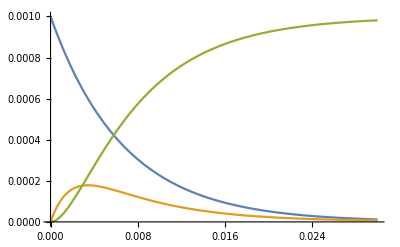

```mathematica
Plot[
bvalsoln, {t, 0, .030},
PlotRange -> All
]
```